#### Data Processing Step

```mathematica
key=Import["key.txt"];
```

```mathematica
key
```

```mathematica
"3a2efab4111941cc887511bd3e860b51"
```

```mathematica
Clear[search];
```

```mathematica
process[url_]:=Module[{image,w,h,min},
Quiet[image=TimeConstrained[Import[url],8,$Failed]];
If[MatchQ[image,_Image],
{w,h}=ImageDimensions[image];
min=Min[{w,h}];
ImageResize[ImageTake[image,{h-min,h+min}/2,{w-min,w+min}/2],{100,100}],
$Failed]
]
```

```mathematica
search[term_String,start_Integer,count_Integer]:=Module[{url,result,json},
url="https://api.cognitive.microsoft.com/bing/v5.0/images/search?q="<>term<>"&count="<>ToString[count]<>"&offset="<>ToString[start]<>"&mkt=en-us&safeSearch=Moderate";
result=URLRead[HTTPRequest[url,<|"Headers"->{"Ocp-Apim-Subscription-Key"->key}|>]];
json=ImportString[result["Body"],"RawJSON"];
process/@Map[#["contentUrl"]&,json["value"]]
];
```

```mathematica
lions=DeleteCases[search["lion",200],$Failed];
```

```mathematica
DumpSave["lions.mx",lions];
```

```mathematica
tigers=DeleteCases[search["tiger",200],$Failed];
```

```mathematica
DumpSave["tigers.mx",tigers];
```

```mathematica
bears=DeleteCases[search["bear",200],$Failed];
```

```mathematica
DumpSave["bears.mx",bears];
```

#### Machine Learning Step

```mathematica
Get["lions.mx"]
```

```mathematica
Get["tigers.mx"]
```

```mathematica
Get["bears.mx"]
```

```mathematica
net=NetChain[{
ConvolutionLayer[20,20],
Ramp,
PoolingLayer[2,2],
ConvolutionLayer[50,5],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"lion","tiger","bear"}}]
]
```

NetChain[]

```mathematica
data=RandomSample[
Flatten[{
Map[#->"lion"&,lions],
Map[#->"tiger"&,tigers],
Map[#->"bear"&,bears]
}]
];
```

```mathematica
RandomSample[data,5]
```

{-Graphics-→bear,-Graphics-→bear,-Graphics-→tiger,-Graphics-→lion,-Graphics-→lion}

```mathematica
Length[data]
```

446

```mathematica
training=Take[data,400];
validation=Take[data,-46];
```

```mathematica
result=NetTrain[net,training,TargetDevice->"GPU",MaxTrainingRounds->100];
```

```mathematica
RandomSample[validation,6]
```

{-Graphics-→lion,-Graphics-→lion,-Graphics-→bear,-Graphics-→tiger,-Graphics-→tiger,-Graphics-→lion}

```mathematica
result[-Graphics-]
```

lion

```mathematica
Dataset[
Map[
<|"image"->First[#],"expected"->Last[#],"predicted"->result[First[#]]|>&,
RandomSample[validation,6]
]
]
```

Dataset[<>]

```mathematica
cm=ClassifierMeasurements[result,validation];
```

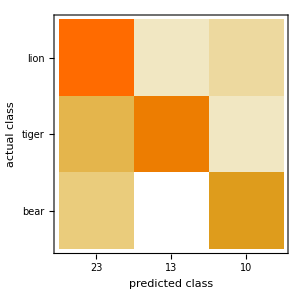

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
Dataset[
Map[
<|"image"->First[#],"expected"->Last[#],"predicted"->result[First[#]]|>&,
validation
]
]
```

Dataset[<>]

```mathematica
result
```

NetChain[]

```mathematica
conv=NetExtract[result,1]
```

None